# Numerical implementation of the Z function

This implementation uses the representation in terms of error functions for small argument |z|<M and asymptotic expansion for argument |z| > M. Now M=4. 
Note: The choice of s in the asymptotic expansion is different from that given in the plasma formulary (their sigma).  Use of their sigma clearly doesn't work for example when Re[z] =0.  Then sigma must be 0 whereas their forumlua would have sigma=1.

### Z function module

```mathematica
Zfun[z0_]:=Module[{M=4.,s,y,q,z2},
z=N[z0];
If[Abs[z]<M,

1.772453851*I* E^(-z^2)(1+ Erf[I z]),	(* error function form  *)
	
	y=Im[z];	(* asymptotic expansion *)
	Which[y==0.,s=1,  y>0,s=0,   y<0,s=2];
	z2=z^2;
	q=(1+1/(2 z2)+3/(4 z2^2)+15/(8 z2^3)+7*15/(16 z2^4))/z;
	1.772453851*I*s*E^(-z2)-q		(* end of asymptotic expansion *)
]	(* end if  *)
]	(* end module *)
```

## Testing of Zfun

```mathematica
Zfun[1+I]
```

-0.369058+0.540145 ⅈ

```mathematica
x={0,.1,1,2,5};
y={0.,.1,2,5};
TableForm[Table[Zfun[x[[i]]+y[[j]]*I],{i,1,5},{j,1,4}]]
```

0.+1.77245 ⅈ | 0.+1.58893 ⅈ | 0.+0.452677 ⅈ | 0.+0.196219 ⅈ
-0.198672+1.75482 ⅈ | -0.167198+1.57479 ⅈ | -0.0189018+0.451937 ⅈ | -0.00377991+0.196148 ⅈ
-1.07616+0.652049 ⅈ | -0.954564+0.661427 ⅈ | -0.164834+0.387268 ⅈ | -0.0365201+0.189294 ⅈ
-0.602681+0.0324636 ⅈ | -0.587715+0.0712551 ⅈ | -0.23251+0.262239 ⅈ | -0.0662039+0.171038 ⅈ
-0.204267+2.46157×10^-11 ⅈ | -0.204176+0.00426596 ⅈ | -0.173678+0.0720393 ⅈ | -0.0989716+0.100969 ⅈ

Test timing for 100 evaluations

```mathematica
Table[Zfun[.1*i*E^(.1*I*i)],{i,0,100}];
```

Time was 8.4 sec

### Plot for real argument

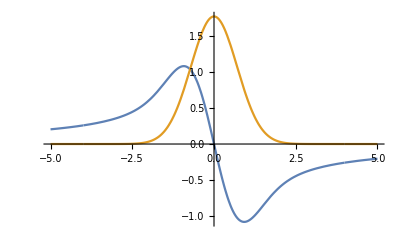

```mathematica
Plot[{Re[Zfun[x]],Im[Zfun[x]]},{x,-5,5},PlotRange->All]
```

## Testing of individual parts

### Erf form

```mathematica
Zf[z_]:=1.772453851*I* E^(-z^2)(1+ Erf[I z])//N
```

```mathematica
Zf[.1*I]
```

0.+1.58893 ⅈ

```mathematica
TableForm[Table[Zf[x[[i]]+y[[j]]*I],{i,1,5},{j,1,4}]]
```

0.+1.77245 ⅈ | 0.+1.58893 ⅈ | 0.+0.452677 ⅈ | 0.+0.196216 ⅈ
-0.198672+1.75482 ⅈ | -0.167198+1.57479 ⅈ | -0.0189018+0.451937 ⅈ | -0.00377898+0.196148 ⅈ
-1.07616+0.652049 ⅈ | -0.954564+0.661427 ⅈ | -0.164834+0.387268 ⅈ | -0.0365178+0.189297 ⅈ
-0.602681+0.0324636 ⅈ | -0.587715+0.0712551 ⅈ | -0.23251+0.262239 ⅈ | -0.0662041+0.171038 ⅈ
-0.204268+2.46157×10^-11 ⅈ | -0.204177+0.00426614 ⅈ | -0.173678+0.072039 ⅈ | -0.0989716+0.100969 ⅈ

These agree to printed accuracy with the Z function tables

### Check Symmetry

```mathematica
fsym[z_]:=(Zfun[Conjugate[z]]+Conjugate[Zfun[-z]])/Abs[Zfun[Conjugate[z]]]
```

```mathematica
TableForm[Table[fsym[i+j*I],{i,0,6,2},{j,-2,4,2}]]
```

0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ

```mathematica
fsym[z_]:=(Zf[Conjugate[z]]+Conjugate[Zf[-z]])/Abs[Zf[Conjugate[z]]]
TableForm[Table[fsym[i+j*I],{i,0,6,2},{j,-2,4,2}]]
```

0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ

### Asymptotic expansion

```mathematica
ZAsymp[z_]:=Module[{s,a,y,q,z2},
			a=Abs[Re[z]];
			y=Im[z];
			Which[y==0.,s=1,  y>0,s=0,   y<0,s=2];
			z2=z^2;
			q=(1+1/(2 z2)+3/(4 z2^2)+15/(8 z2^3)+7*15/(16 z2^4))/z;
			N[1.772453851*I*s*E^(-z2)-q]
			]
```

```mathematica
TableForm[Table[ZAsymp[x[[i]]+y[[j]]*I],{i,2,5},{j,2,4}]]
```

-2.06241×10^8+2.03897×10^8 ⅈ | -0.0219314+0.457526 ⅈ | -0.00377991+0.196148 ⅈ
-7.40646+6.66096 ⅈ | -0.162507+0.38714 ⅈ | -0.0365201+0.189294 ⅈ
-0.607947+0.0504765 ⅈ | -0.232761+0.26218 ⅈ | -0.0662039+0.171038 ⅈ
-0.204176+0.00426596 ⅈ | -0.173678+0.0720393 ⅈ | -0.0989716+0.100969 ⅈ

This also checks with Z function table

Check Symmetry

```mathematica
fsym[z_]:=(ZAsymp[Conjugate[z]]+Conjugate[ZAsymp[-z]])/Abs[ZAsymp[Conjugate[z]]]
```

```mathematica
TableForm[Table[fsym[i+j*I],{i,-4,8,.51},{j,-5,5,2.5}]]
```

0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ

### Compare Erf form with asymptotic expansion

### Real argument

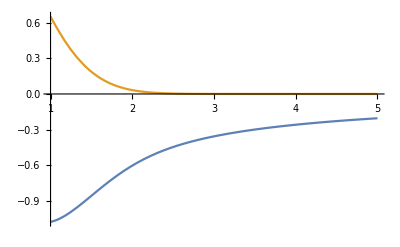

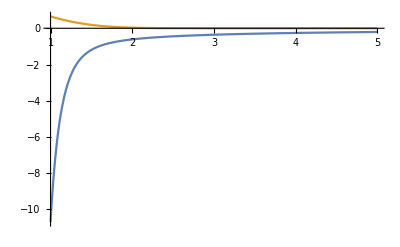

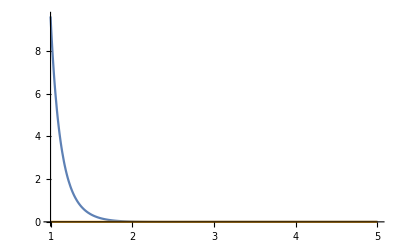

```mathematica
Plot[{Re[Zf[x]],Im[Zf[x]]},{x,1,5},PlotRange->All]
Plot[{Re[ZAsymp[x]],Im[ZAsymp[x]]},{x,1,5},PlotRange->All]
Plot[{Re[Zf[x]-ZAsymp[x]],Im[Zf[x]-ZAsymp[x]]},{x,1,5},PlotRange->All]
```

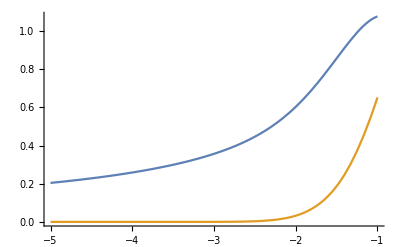

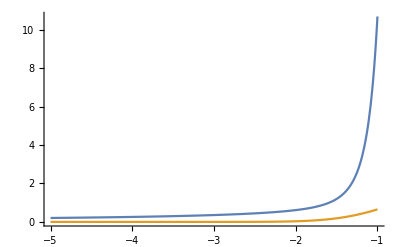

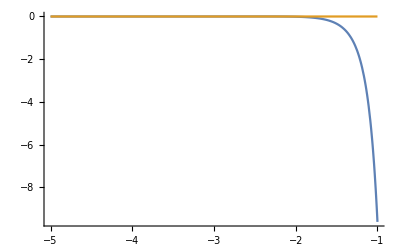

```mathematica
Plot[{Re[Zf[x]],Im[Zf[x]]},{x,-5,-1},PlotRange->All]
Plot[{Re[ZAsymp[x]],Im[ZAsymp[x]]},{x,-5,-1},PlotRange->All]
Plot[{Re[Zf[x]-ZAsymp[x]],Im[Zf[x]-ZAsymp[x]]},{x,-5,-1},PlotRange->All]
```

### Complex argument

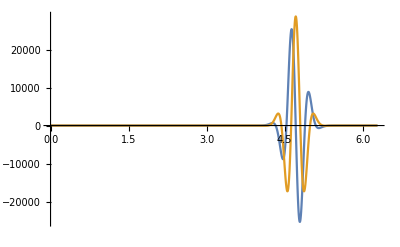

-Graphics-

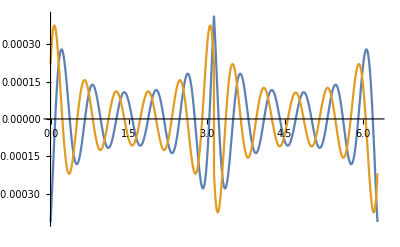

```mathematica
r=3.;
Plot[{Re[Zf[r*Exp[ⅈ theta]]],Im[Zf[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[ZAsymp[r*Exp[ⅈ theta]]],Im[ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[Zf[r*Exp[ⅈ theta]]-ZAsymp[r*Exp[ⅈ theta]]],Im[Zf[r*Exp[ⅈ theta]]-ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
```

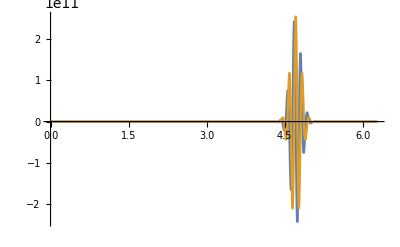

-Graphics-

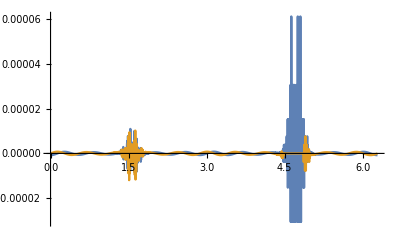

```mathematica
r=5.;
Plot[{Re[Zf[r*Exp[ⅈ theta]]],Im[Zf[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[ZAsymp[r*Exp[ⅈ theta]]],Im[ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[Zf[r*Exp[ⅈ theta]]-ZAsymp[r*Exp[ⅈ theta]]],Im[Zf[r*Exp[ⅈ theta]]-ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
```

### Which raises the question : Does the Erf form have the wiggles at about 1.5 or not?

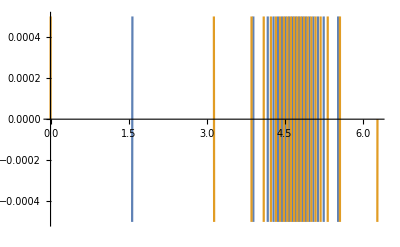

```mathematica
r=5.;
Plot[{Re[Zf[r*Exp[ⅈ theta]]],Im[Zf[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange->{-.0005, .0005}]
```

### Yes, it does . Does my form of the asymptotic expansion have them?

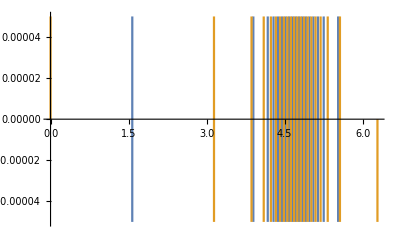

```mathematica
r=5.;
Plot[{Re[ZAsymp[r*Exp[ⅈ theta]]],Im[ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange->{-.00005, .00005}]
```

### Yes, it does . So how well do they agree on the wiggles?

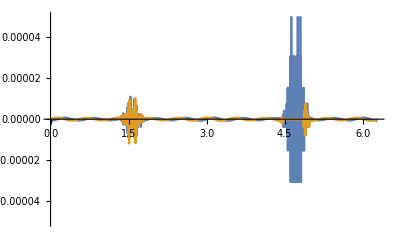

```mathematica
r=5.;
Plot[{Re[Zf[r*Exp[ⅈ theta]]-ZAsymp[r*Exp[ⅈ theta]]],Im[Zf[r*Exp[ⅈ theta]]-ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange->{-.00005, .00005}]
```

### They agree very well. What happens if we use the choice of s in the asymptotic expansion given in the NRL formulary?

```mathematica
ZAsymp2[z_Complex]:=Module[{s,a,y,q,z2},
			a=Abs[Re[z]];
			y=Im[z];
			Which[y>1/a,s=0,  Abs[y]<1/a,s=1,   y<-1/a,s=2];
			z2=z^2;
			q=(1+1/(2 z2)+3/(4 z2^2)+15/(8 z2^3)+7*15/(16 z2^4))/z;
			N[1.772453851*I*s*E^(-z2)-q]
			]
```

-Graphics-

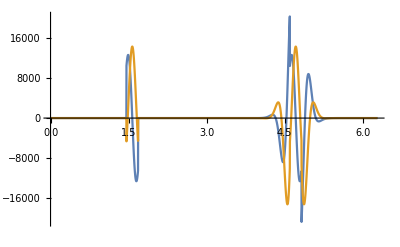

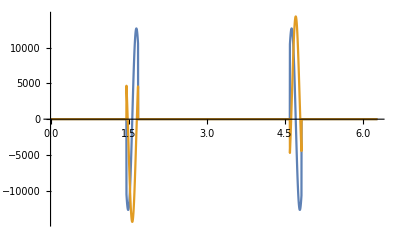

```mathematica
r=3.;
Plot[{Re[ZAsymp[r*Exp[ⅈ theta]]],Im[ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[ZAsymp2[r*Exp[ⅈ theta]]],Im[ZAsymp2[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[ZAsymp[r*Exp[ⅈ theta]]-ZAsymp2[r*Exp[ⅈ theta]]],Im[ZAsymp[r*Exp[ⅈ theta]]-ZAsymp2[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
```

-Graphics-

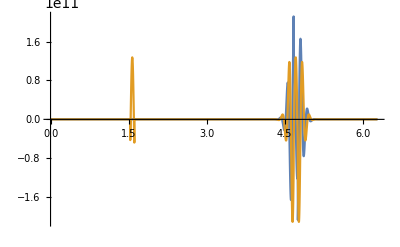

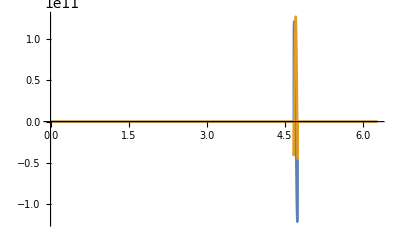

```mathematica
r=5.;
Plot[{Re[ZAsymp[r*Exp[ⅈ theta]]],Im[ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[ZAsymp2[r*Exp[ⅈ theta]]],Im[ZAsymp2[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[ZAsymp[r*Exp[ⅈ theta]]-ZAsymp2[r*Exp[ⅈ theta]]],Im[ZAsymp[r*Exp[ⅈ theta]]-ZAsymp2[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
```

## Set transition to asymptotics small, M=1.5 and look at break

```mathematica
Zfun[z0_]:=Module[{M=1.5,s,y,q,z2},
z=N[z0];
If[Abs[z]<M,

1.772453851*I* E^(-z^2)(1+ Erf[I z]),	(* error function form  *)
	
	y=Im[z];	(* asymptotic expansion *)
	Which[y==0.,s=1,  y>0,s=0,   y<0,s=2];
	z2=z^2;
	q=(1+1/(2 z2)+3/(4 z2^2)+15/(8 z2^3)+7*15/(16 z2^4))/z;
	1.772453851*I*s*E^(-z2)-q		(* end of asymptotic expansion *)
]	(* end if  *)
]	(* end module *)
```

```mathematica
zf=Table[{z,Zfun[z]},{z,-4,4,.001}];
ComplexVectorListPlot[zf,"z","Zfun[z]", PlotRange->All]
```

### M = 2.

```mathematica
Zfun[z0_]:=Module[{M=2.,s,y,q,z2},
z=N[z0];
If[Abs[z]<M,

1.772453851*I* E^(-z^2)(1+ Erf[I z]),	(* error function form  *)
	
	y=Im[z];	(* asymptotic expansion *)
	Which[y==0.,s=1,  y>0,s=0,   y<0,s=2];
	z2=z^2;
	q=(1+1/(2 z2)+3/(4 z2^2)+15/(8 z2^3)+7*15/(16 z2^4))/z;
	1.772453851*I*s*E^(-z2)-q		(* end of asymptotic expansion *)
]	(* end if  *)
]	(* end module *)
```

```mathematica
zf=Table[{z,Zfun[z]},{z,-4,4,.01}];
ComplexVectorListPlot[zf,"z","Zfun[z]", PlotRange->All]
```

ComplexVectorListPlot[{{-4.,0.258684+1.99463×10^-7 ⅈ},{-3.99,0.259382+2.16055×10^-7 ⅈ},{-3.98,0.260083+2.33979×10^-7 ⅈ},{-3.97,0.260788+2.5334×10^-7 ⅈ},{-3.96,0.261497+2.74247×10^-7 ⅈ},{-3.95,0.26221+2.96821×10^-7 ⅈ},{-3.94,0.262928+3.21189×10^-7 ⅈ},{-3.93,0.263649+3.47488×10^-7 ⅈ},{-3.92,0.264375+3.75865×10^-7 ⅈ},{-3.91,0.265105+4.06478×10^-7 ⅈ},{-3.9,0.265839+4.39497×10^-7 ⅈ},{-3.89,0.266577+4.75103×10^-7 ⅈ},{-3.88,0.267319+5.1349×10^-7 ⅈ},{-3.87,0.268066+5.54868×10^-7 ⅈ},{-3.86,0.268818+5.99461×10^-7 ⅈ},{-3.85,0.269573+6.47508×10^-7 ⅈ},{-3.84,0.270334+6.99266×10^-7 ⅈ},{-3.83,0.271098+7.5501×10^-7 ⅈ},{-3.82,0.271868+8.15035×10^-7 ⅈ},{-3.81,0.272642+8.79656×10^-7 ⅈ},{-3.8,0.27342+9.49211×10^-7 ⅈ},{-3.79,0.274203+1.02406×10^-6 ⅈ},{-3.78,0.274991+1.10459×10^-6 ⅈ},{-3.77,0.275784+1.19122×10^-6 ⅈ},{-3.76,0.276582+1.28438×10^-6 ⅈ},{-3.75,0.277384+1.38455×10^-6 ⅈ},{-3.74,0.278191+1.49224×10^-6 ⅈ},{-3.73,0.279004+1.60797×10^-6 ⅈ},{-3.72,0.279821+1.73234×10^-6 ⅈ},{-3.71,0.280643+1.86596×10^-6 ⅈ},{-3.7,0.281471+2.00948×10^-6 ⅈ},{-3.69,0.282304+2.1636×10^-6 ⅈ},{-3.68,0.283141+2.32909×10^-6 ⅈ},{-3.67,0.283985+2.50672×10^-6 ⅈ},{-3.66,0.284833+2.69737×10^-6 ⅈ},{-3.65,0.285687+2.90193×10^-6 ⅈ},{-3.64,0.286546+3.12138×10^-6 ⅈ},{-3.63,0.287411+3.35676×10^-6 ⅈ},{-3.62,0.288281+3.60916×10^-6 ⅈ},{-3.61,0.289157+3.87977×10^-6 ⅈ},{-3.6,0.290039+4.16983×10^-6 ⅈ},{-3.59,0.290926+4.48068×10^-6 ⅈ},{-3.58,0.291819+4.81375×10^-6 ⅈ},{-3.57,0.292718+5.17053×10^-6 ⅈ},{-3.56,0.293623+5.55265×10^-6 ⅈ},{-3.55,0.294533+5.96182×10^-6 ⅈ},{-3.54,0.29545+6.39986×10^-6 ⅈ},{-3.53,0.296373+6.8687×10^-6 ⅈ},{-3.52,0.297302+7.37043×10^-6 ⅈ},{-3.51,0.298237+7.90721×10^-6 ⅈ},{-3.5,0.299179+8.4814×10^-6 ⅈ},{-3.49,0.300127+9.09546×10^-6 ⅈ},{-3.48,0.301081+9.75203×10^-6 ⅈ},{-3.47,0.302042+0.0000104539 ⅈ},{-3.46,0.303009+0.0000112041 ⅈ},{-3.45,0.303983+0.0000120056 ⅈ},{-3.44,0.304964+0.000012862 ⅈ},{-3.43,0.305951+0.0000137767 ⅈ},{-3.42,0.306945+0.0000147534 ⅈ},{-3.41,0.307947+0.0000157963 ⅈ},{-3.4,0.308955+0.0000169095 ⅈ},{-3.39,0.30997+0.0000180975 ⅈ},{-3.38,0.310993+0.0000193652 ⅈ},{-3.37,0.312022+0.0000207174 ⅈ},{-3.36,0.31306+0.0000221597 ⅈ},{-3.35,0.314104+0.0000236976 ⅈ},{-3.34,0.315156+0.0000253372 ⅈ},{-3.33,0.316216+0.0000270849 ⅈ},{-3.32,0.317283+0.0000289473 ⅈ},{-3.31,0.318358+0.0000309315 ⅈ},{-3.3,0.319441+0.0000330452 ⅈ},{-3.29,0.320532+0.0000352962 ⅈ},{-3.28,0.321631+0.000037693 ⅈ},{-3.27,0.322739+0.0000402446 ⅈ},{-3.26,0.323854+0.0000429603 ⅈ},{-3.25,0.324978+0.00004585 ⅈ},{-3.24,0.32611+0.0000489244 ⅈ},{-3.23,0.327251+0.0000521944 ⅈ},{-3.22,0.328401+0.0000556719 ⅈ},{-3.21,0.329559+0.0000593692 ⅈ},{-3.2,0.330726+0.0000632994 ⅈ},{-3.19,0.331902+0.0000674762 ⅈ},{-3.18,0.333088+0.0000719143 ⅈ},{-3.17,0.334282+0.000076629 ⅈ},{-3.16,0.335486+0.0000816364 ⅈ},{-3.15,0.3367+0.0000869537 ⅈ},{-3.14,0.337923+0.0000925987 ⅈ},{-3.13,0.339156+0.0000985906 ⅈ},{-3.12,0.340398+0.000104949 ⅈ},{-3.11,0.341651+0.000111695 ⅈ},{-3.1,0.342914+0.000118852 ⅈ},{-3.09,0.344187+0.000126441 ⅈ},{-3.08,0.34547+0.000134488 ⅈ},{-3.07,0.346764+0.000143019 ⅈ},{-3.06,0.348069+0.00015206 ⅈ},{-3.05,0.349384+0.000161641 ⅈ},{-3.04,0.35071+0.00017179 ⅈ},{-3.03,0.352048+0.000182541 ⅈ},{-3.02,0.353397+0.000193926 ⅈ},{-3.01,0.354757+0.000205979 ⅈ},{-3.,0.356129+0.000218738 ⅈ},{-2.99,0.357513+0.000232241 ⅈ},{-2.98,0.358908+0.000246528 ⅈ},{-2.97,0.360316+0.000261642 ⅈ},{-2.96,0.361736+0.000277626 ⅈ},{-2.95,0.363168+0.000294528 ⅈ},{-2.94,0.364614+0.000312397 ⅈ},{-2.93,0.366072+0.000331284 ⅈ},{-2.92,0.367543+0.000351242 ⅈ},{-2.91,0.369027+0.000372328 ⅈ},{-2.9,0.370525+0.000394601 ⅈ},{-2.89,0.372036+0.000418123 ⅈ},{-2.88,0.373561+0.000442958 ⅈ},{-2.87,0.3751+0.000469175 ⅈ},{-2.86,0.376654+0.000496844 ⅈ},{-2.85,0.378222+0.000526039 ⅈ},{-2.84,0.379804+0.000556839 ⅈ},{-2.83,0.381402+0.000589324 ⅈ},{-2.82,0.383015+0.000623579 ⅈ},{-2.81,0.384644+0.000659694 ⅈ},{-2.8,0.386288+0.00069776 ⅈ},{-2.79,0.387948+0.000737876 ⅈ},{-2.78,0.389624+0.000780142 ⅈ},{-2.77,0.391317+0.000824664 ⅈ},{-2.76,0.393026+0.000871552 ⅈ},{-2.75,0.394753+0.000920922 ⅈ},{-2.74,0.396497+0.000972894 ⅈ},{-2.73,0.398259+0.00102759 ⅈ},{-2.72,0.400038+0.00108515 ⅈ},{-2.71,0.401836+0.00114571 ⅈ},{-2.7,0.403653+0.00120939 ⅈ},{-2.69,0.405488+0.00127637 ⅈ},{-2.68,0.407343+0.00134678 ⅈ},{-2.67,0.409218+0.0014208 ⅈ},{-2.66,0.411112+0.00149858 ⅈ},{-2.65,0.413027+0.00158031 ⅈ},{-2.64,0.414962+0.00166616 ⅈ},{-2.63,0.416919+0.00175632 ⅈ},{-2.62,0.418897+0.00185099 ⅈ},{-2.61,0.420897+0.00195037 ⅈ},{-2.6,0.422919+0.00205468 ⅈ},{-2.59,0.424964+0.00216413 ⅈ},{-2.58,0.427032+0.00227896 ⅈ},{-2.57,0.429124+0.0023994 ⅈ},{-2.56,0.43124+0.0025257 ⅈ},{-2.55,0.433381+0.00265812 ⅈ},{-2.54,0.435547+0.00279692 ⅈ},{-2.53,0.437738+0.00294238 ⅈ},{-2.52,0.439956+0.00309479 ⅈ},{-2.51,0.442201+0.00325444 ⅈ},{-2.5,0.444472+0.00342164 ⅈ},{-2.49,0.446772+0.00359671 ⅈ},{-2.48,0.4491+0.00377999 ⅈ},{-2.47,0.451457+0.0039718 ⅈ},{-2.46,0.453844+0.00417252 ⅈ},{-2.45,0.456261+0.0043825 ⅈ},{-2.44,0.458709+0.00460213 ⅈ},{-2.43,0.461189+0.00483181 ⅈ},{-2.42,0.463702+0.00507192 ⅈ},{-2.41,0.466247+0.00532291 ⅈ},{-2.4,0.468827+0.0055852 ⅈ},{-2.39,0.471441+0.00585924 ⅈ},{-2.38,0.474091+0.0061455 ⅈ},{-2.37,0.476778+0.00644446 ⅈ},{-2.36,0.479501+0.0067566 ⅈ},{-2.35,0.482263+0.00708245 ⅈ},{-2.34,0.485064+0.00742253 ⅈ},{-2.33,0.487906+0.00777739 ⅈ},{-2.32,0.490788+0.00814757 ⅈ},{-2.31,0.493712+0.00853368 ⅈ},{-2.3,0.49668+0.00893629 ⅈ},{-2.29,0.499693+0.00935602 ⅈ},{-2.28,0.50275+0.00979351 ⅈ},{-2.27,0.505855+0.0102494 ⅈ},{-2.26,0.509008+0.0107244 ⅈ},{-2.25,0.51221+0.0112191 ⅈ},{-2.24,0.515462+0.0117343 ⅈ},{-2.23,0.518767+0.0122708 ⅈ},{-2.22,0.522125+0.0128292 ⅈ},{-2.21,0.525538+0.0134103 ⅈ},{-2.2,0.529008+0.0140149 ⅈ},{-2.19,0.532536+0.0146438 ⅈ},{-2.18,0.536125+0.015298 ⅈ},{-2.17,0.539774+0.0159781 ⅈ},{-2.16,0.543488+0.0166852 ⅈ},{-2.15,0.547267+0.01742 ⅈ},{-2.14,0.551113+0.0181836 ⅈ},{-2.13,0.555029+0.0189769 ⅈ},{-2.12,0.559017+0.0198008 ⅈ},{-2.11,0.563079+0.0206563 ⅈ},{-2.1,0.567217+0.0215445 ⅈ},{-2.09,0.571434+0.0224664 ⅈ},{-2.08,0.575732+0.023423 ⅈ},{-2.07,0.580115+0.0244155 ⅈ},{-2.06,0.584585+0.025445 ⅈ},{-2.05,0.589144+0.0265126 ⅈ},{-2.04,0.593797+0.0276194 ⅈ},{-2.03,0.598545+0.0287668 ⅈ},{-2.02,0.603394+0.0299557 ⅈ},{-2.01,0.608345+0.0311876 ⅈ},{-2.,0.613403+0.0324636 ⅈ},{-1.99,0.60681+0.0337851 ⅈ},{-1.98,0.610983+0.0351534 ⅈ},{-1.97,0.6152+0.0365697 ⅈ},{-1.96,0.619461+0.0380355 ⅈ},{-1.95,0.623765+0.0395522 ⅈ},{-1.94,0.628114+0.0411211 ⅈ},{-1.93,0.632507+0.0427436 ⅈ},{-1.92,0.636944+0.0444214 ⅈ},{-1.91,0.641424+0.0461557 ⅈ},{-1.9,0.645949+0.0479482 ⅈ},{-1.89,0.650516+0.0498003 ⅈ},{-1.88,0.655128+0.0517136 ⅈ},{-1.87,0.659782+0.0536896 ⅈ},{-1.86,0.664479+0.0557301 ⅈ},{-1.85,0.669219+0.0578365 ⅈ},{-1.84,0.674001+0.0600105 ⅈ},{-1.83,0.678825+0.0622538 ⅈ},{-1.82,0.683691+0.0645681 ⅈ},{-1.81,0.688598+0.066955 ⅈ},{-1.8,0.693546+0.0694162 ⅈ},{-1.79,0.698533+0.0719535 ⅈ},{-1.78,0.70356+0.0745687 ⅈ},{-1.77,0.708626+0.0772634 ⅈ},{-1.76,0.713731+0.0800395 ⅈ},{-1.75,0.718873+0.0828988 ⅈ},{-1.74,0.724052+0.085843 ⅈ},{-1.73,0.729267+0.0888741 ⅈ},{-1.72,0.734517+0.0919937 ⅈ},{-1.71,0.739801+0.0952038 ⅈ},{-1.7,0.745119+0.0985063 ⅈ},{-1.69,0.750469+0.101903 ⅈ},{-1.68,0.75585+0.105396 ⅈ},{-1.67,0.761261+0.108986 ⅈ},{-1.66,0.766702+0.112676 ⅈ},{-1.65,0.77217+0.116468 ⅈ},{-1.64,0.777665+0.120364 ⅈ},{-1.63,0.783184+0.124365 ⅈ},{-1.62,0.788728+0.128473 ⅈ},{-1.61,0.794293+0.132691 ⅈ},{-1.6,0.79988+0.137019 ⅈ},{-1.59,0.805485+0.14146 ⅈ},{-1.58,0.811108+0.146017 ⅈ},{-1.57,0.816747+0.150689 ⅈ},{-1.56,0.822399+0.15548 ⅈ},{-1.55,0.828064+0.160392 ⅈ},{-1.54,0.833738+0.165425 ⅈ},{-1.53,0.839421+0.170583 ⅈ},{-1.52,0.84511+0.175866 ⅈ},{-1.51,0.850803+0.181276 ⅈ},{-1.5,0.856498+0.186815 ⅈ},{-1.49,0.862192+0.192485 ⅈ},{-1.48,0.867884+0.198288 ⅈ},{-1.47,0.87357+0.204225 ⅈ},{-1.46,0.879249+0.210297 ⅈ},{-1.45,0.884918+0.216506 ⅈ},{-1.44,0.890573+0.222855 ⅈ},{-1.43,0.896214+0.229343 ⅈ},{-1.42,0.901836+0.235974 ⅈ},{-1.41,0.907437+0.242747 ⅈ},{-1.4,0.913014+0.249665 ⅈ},{-1.39,0.918565+0.256729 ⅈ},{-1.38,0.924086+0.26394 ⅈ},{-1.37,0.929573+0.271299 ⅈ},{-1.36,0.935025+0.278807 ⅈ},{-1.35,0.940438+0.286466 ⅈ},{-1.34,0.945808+0.294277 ⅈ},{-1.33,0.951132+0.30224 ⅈ},{-1.32,0.956407+0.310356 ⅈ},{-1.31,0.961629+0.318627 ⅈ},{-1.3,0.966795+0.327052 ⅈ},{-1.29,0.971901+0.335634 ⅈ},{-1.28,0.976944+0.344371 ⅈ},{-1.27,0.981919+0.353266 ⅈ},{-1.26,0.986824+0.362317 ⅈ},{-1.25,0.991654+0.371527 ⅈ},{-1.24,0.996406+0.380894 ⅈ},{-1.23,1.00107+0.390419 ⅈ},{-1.22,1.00566+0.400102 ⅈ},{-1.21,1.01015+0.409944 ⅈ},{-1.2,1.01455+0.419944 ⅈ},{-1.19,1.01885+0.430101 ⅈ},{-1.18,1.02304+0.440416 ⅈ},{-1.17,1.02713+0.450889 ⅈ},{-1.16,1.03111+0.461518 ⅈ},{-1.15,1.03497+0.472303 ⅈ},{-1.14,1.03872+0.483243 ⅈ},{-1.13,1.04234+0.494338 ⅈ},{-1.12,1.04583+0.505587 ⅈ},{-1.11,1.04919+0.516988 ⅈ},{-1.1,1.05241+0.528541 ⅈ},{-1.09,1.0555+0.540244 ⅈ},{-1.08,1.05843+0.552095 ⅈ},{-1.07,1.06122+0.564094 ⅈ},{-1.06,1.06385+0.576238 ⅈ},{-1.05,1.06632+0.588525 ⅈ},{-1.04,1.06863+0.600955 ⅈ},{-1.03,1.07078+0.613525 ⅈ},{-1.02,1.07275+0.626232 ⅈ},{-1.01,1.07454+0.639074 ⅈ},{-1.,1.07616+0.652049 ⅈ},{-0.99,1.07759+0.665155 ⅈ},{-0.98,1.07883+0.678389 ⅈ},{-0.97,1.07988+0.691747 ⅈ},{-0.96,1.08073+0.705227 ⅈ},{-0.95,1.08138+0.718827 ⅈ},{-0.94,1.08182+0.732542 ⅈ},{-0.93,1.08205+0.746369 ⅈ},{-0.92,1.08207+0.760305 ⅈ},{-0.91,1.08187+0.774347 ⅈ},{-0.9,1.08145+0.78849 ⅈ},{-0.89,1.0808+0.802731 ⅈ},{-0.88,1.07992+0.817066 ⅈ},{-0.87,1.07881+0.831491 ⅈ},{-0.86,1.07747+0.846001 ⅈ},{-0.85,1.07588+0.860592 ⅈ},{-0.84,1.07404+0.875259 ⅈ},{-0.83,1.07196+0.889999 ⅈ},{-0.82,1.06963+0.904806 ⅈ},{-0.81,1.06705+0.919675 ⅈ},{-0.8,1.0642+0.934601 ⅈ},{-0.79,1.0611+0.94958 ⅈ},{-0.78,1.05773+0.964606 ⅈ},{-0.77,1.0541+0.979674 ⅈ},{-0.76,1.0502+0.994779 ⅈ},{-0.75,1.04603+1.00991 ⅈ},{-0.74,1.04158+1.02507 ⅈ},{-0.73,1.03686+1.04025 ⅈ},{-0.72,1.03185+1.05545 ⅈ},{-0.71,1.02657+1.07065 ⅈ},{-0.7,1.02101+1.08585 ⅈ},{-0.69,1.01516+1.10105 ⅈ},{-0.68,1.00903+1.11624 ⅈ},{-0.67,1.0026+1.13141 ⅈ},{-0.66,0.995895+1.14656 ⅈ},{-0.65,0.988896+1.16168 ⅈ},{-0.64,0.981606+1.17676 ⅈ},{-0.63,0.974025+1.1918 ⅈ},{-0.62,0.966152+1.20679 ⅈ},{-0.61,0.957986+1.22173 ⅈ},{-0.6,0.949526+1.2366 ⅈ},{-0.59,0.940774+1.2514 ⅈ},{-0.58,0.931729+1.26613 ⅈ},{-0.57,0.92239+1.28077 ⅈ},{-0.56,0.912759+1.29533 ⅈ},{-0.55,0.902836+1.30979 ⅈ},{-0.54,0.892622+1.32414 ⅈ},{-0.53,0.882117+1.33839 ⅈ},{-0.52,0.871323+1.35251 ⅈ},{-0.51,0.860241+1.36652 ⅈ},{-0.5,0.848873+1.38039 ⅈ},{-0.49,0.837219+1.39412 ⅈ},{-0.48,0.825283+1.40771 ⅈ},{-0.47,0.813065+1.42115 ⅈ},{-0.46,0.800569+1.43443 ⅈ},{-0.45,0.787797+1.44754 ⅈ},{-0.44,0.774751+1.46048 ⅈ},{-0.43,0.761433+1.47324 ⅈ},{-0.42,0.747848+1.48582 ⅈ},{-0.41,0.733998+1.4982 ⅈ},{-0.4,0.719887+1.51039 ⅈ},{-0.39,0.705518+1.52236 ⅈ},{-0.38,0.690894+1.53413 ⅈ},{-0.37,0.676021+1.54568 ⅈ},{-0.36,0.660901+1.55701 ⅈ},{-0.35,0.645539+1.5681 ⅈ},{-0.34,0.62994+1.57896 ⅈ},{-0.33,0.614108+1.58957 ⅈ},{-0.32,0.598048+1.59994 ⅈ},{-0.31,0.581765+1.61005 ⅈ},{-0.3,0.565263+1.6199 ⅈ},{-0.29,0.548549+1.62949 ⅈ},{-0.28,0.531628+1.6388 ⅈ},{-0.27,0.514506+1.64784 ⅈ},{-0.26,0.497187+1.6566 ⅈ},{-0.25,0.479678+1.66507 ⅈ},{-0.24,0.461986+1.67325 ⅈ},{-0.23,0.444115+1.68113 ⅈ},{-0.22,0.426074+1.68871 ⅈ},{-0.21,0.407867+1.69599 ⅈ},{-0.2,0.389502+1.70295 ⅈ},{-0.19,0.370985+1.70961 ⅈ},{-0.18,0.352324+1.71595 ⅈ},{-0.17,0.333524+1.72196 ⅈ},{-0.16,0.314594+1.72765 ⅈ},{-0.15,0.29554+1.73302 ⅈ},{-0.14,0.27637+1.73805 ⅈ},{-0.13,0.25709+1.74275 ⅈ},{-0.12,0.237709+1.74711 ⅈ},{-0.11,0.218234+1.75114 ⅈ},{-0.1,0.198672+1.75482 ⅈ},{-0.09,0.179031+1.75815 ⅈ},{-0.08,0.159319+1.76115 ⅈ},{-0.07,0.139544+1.76379 ⅈ},{-0.06,0.119712+1.76608 ⅈ},{-0.05,0.0998335+1.76803 ⅈ},{-0.04,0.0799147+1.76962 ⅈ},{-0.03,0.059964+1.77086 ⅈ},{-0.02,0.0399893+1.77175 ⅈ},{-0.01,0.0199987+1.77228 ⅈ},{0.,0.+1.77245 ⅈ},{0.01,-0.0199987+1.77228 ⅈ},{0.02,-0.0399893+1.77175 ⅈ},{0.03,-0.059964+1.77086 ⅈ},{0.04,-0.0799147+1.76962 ⅈ},{0.05,-0.0998335+1.76803 ⅈ},{0.06,-0.119712+1.76608 ⅈ},{0.07,-0.139544+1.76379 ⅈ},{0.08,-0.159319+1.76115 ⅈ},{0.09,-0.179031+1.75815 ⅈ},{0.1,-0.198672+1.75482 ⅈ},{0.11,-0.218234+1.75114 ⅈ},{0.12,-0.237709+1.74711 ⅈ},{0.13,-0.25709+1.74275 ⅈ},{0.14,-0.27637+1.73805 ⅈ},{0.15,-0.29554+1.73302 ⅈ},{0.16,-0.314594+1.72765 ⅈ},{0.17,-0.333524+1.72196 ⅈ},{0.18,-0.352324+1.71595 ⅈ},{0.19,-0.370985+1.70961 ⅈ},{0.2,-0.389502+1.70295 ⅈ},{0.21,-0.407867+1.69599 ⅈ},{0.22,-0.426074+1.68871 ⅈ},{0.23,-0.444115+1.68113 ⅈ},{0.24,-0.461986+1.67325 ⅈ},{0.25,-0.479678+1.66507 ⅈ},{0.26,-0.497187+1.6566 ⅈ},{0.27,-0.514506+1.64784 ⅈ},{0.28,-0.531628+1.6388 ⅈ},{0.29,-0.548549+1.62949 ⅈ},{0.3,-0.565263+1.6199 ⅈ},{0.31,-0.581765+1.61005 ⅈ},{0.32,-0.598048+1.59994 ⅈ},{0.33,-0.614108+1.58957 ⅈ},{0.34,-0.62994+1.57896 ⅈ},{0.35,-0.645539+1.5681 ⅈ},{0.36,-0.660901+1.55701 ⅈ},{0.37,-0.676021+1.54568 ⅈ},{0.38,-0.690894+1.53413 ⅈ},{0.39,-0.705518+1.52236 ⅈ},{0.4,-0.719887+1.51039 ⅈ},{0.41,-0.733998+1.4982 ⅈ},{0.42,-0.747848+1.48582 ⅈ},{0.43,-0.761433+1.47324 ⅈ},{0.44,-0.774751+1.46048 ⅈ},{0.45,-0.787797+1.44754 ⅈ},{0.46,-0.800569+1.43443 ⅈ},{0.47,-0.813065+1.42115 ⅈ},{0.48,-0.825283+1.40771 ⅈ},{0.49,-0.837219+1.39412 ⅈ},{0.5,-0.848873+1.38039 ⅈ},{0.51,-0.860241+1.36652 ⅈ},{0.52,-0.871323+1.35251 ⅈ},{0.53,-0.882117+1.33839 ⅈ},{0.54,-0.892622+1.32414 ⅈ},{0.55,-0.902836+1.30979 ⅈ},{0.56,-0.912759+1.29533 ⅈ},{0.57,-0.92239+1.28077 ⅈ},{0.58,-0.931729+1.26613 ⅈ},{0.59,-0.940774+1.2514 ⅈ},{0.6,-0.949526+1.2366 ⅈ},{0.61,-0.957986+1.22173 ⅈ},{0.62,-0.966152+1.20679 ⅈ},{0.63,-0.974025+1.1918 ⅈ},{0.64,-0.981606+1.17676 ⅈ},{0.65,-0.988896+1.16168 ⅈ},{0.66,-0.995895+1.14656 ⅈ},{0.67,-1.0026+1.13141 ⅈ},{0.68,-1.00903+1.11624 ⅈ},{0.69,-1.01516+1.10105 ⅈ},{0.7,-1.02101+1.08585 ⅈ},{0.71,-1.02657+1.07065 ⅈ},{0.72,-1.03185+1.05545 ⅈ},{0.73,-1.03686+1.04025 ⅈ},{0.74,-1.04158+1.02507 ⅈ},{0.75,-1.04603+1.00991 ⅈ},{0.76,-1.0502+0.994779 ⅈ},{0.77,-1.0541+0.979674 ⅈ},{0.78,-1.05773+0.964606 ⅈ},{0.79,-1.0611+0.94958 ⅈ},{0.8,-1.0642+0.934601 ⅈ},{0.81,-1.06705+0.919675 ⅈ},{0.82,-1.06963+0.904806 ⅈ},{0.83,-1.07196+0.889999 ⅈ},{0.84,-1.07404+0.875259 ⅈ},{0.85,-1.07588+0.860592 ⅈ},{0.86,-1.07747+0.846001 ⅈ},{0.87,-1.07881+0.831491 ⅈ},{0.88,-1.07992+0.817066 ⅈ},{0.89,-1.0808+0.802731 ⅈ},{0.9,-1.08145+0.78849 ⅈ},{0.91,-1.08187+0.774347 ⅈ},{0.92,-1.08207+0.760305 ⅈ},{0.93,-1.08205+0.746369 ⅈ},{0.94,-1.08182+0.732542 ⅈ},{0.95,-1.08138+0.718827 ⅈ},{0.96,-1.08073+0.705227 ⅈ},{0.97,-1.07988+0.691747 ⅈ},{0.98,-1.07883+0.678389 ⅈ},{0.99,-1.07759+0.665155 ⅈ},{1.,-1.07616+0.652049 ⅈ},{1.01,-1.07454+0.639074 ⅈ},{1.02,-1.07275+0.626232 ⅈ},{1.03,-1.07078+0.613525 ⅈ},{1.04,-1.06863+0.600955 ⅈ},{1.05,-1.06632+0.588525 ⅈ},{1.06,-1.06385+0.576238 ⅈ},{1.07,-1.06122+0.564094 ⅈ},{1.08,-1.05843+0.552095 ⅈ},{1.09,-1.0555+0.540244 ⅈ},{1.1,-1.05241+0.528541 ⅈ},{1.11,-1.04919+0.516988 ⅈ},{1.12,-1.04583+0.505587 ⅈ},{1.13,-1.04234+0.494338 ⅈ},{1.14,-1.03872+0.483243 ⅈ},{1.15,-1.03497+0.472303 ⅈ},{1.16,-1.03111+0.461518 ⅈ},{1.17,-1.02713+0.450889 ⅈ},{1.18,-1.02304+0.440416 ⅈ},{1.19,-1.01885+0.430101 ⅈ},{1.2,-1.01455+0.419944 ⅈ},{1.21,-1.01015+0.409944 ⅈ},{1.22,-1.00566+0.400102 ⅈ},{1.23,-1.00107+0.390419 ⅈ},{1.24,-0.996406+0.380894 ⅈ},{1.25,-0.991654+0.371527 ⅈ},{1.26,-0.986824+0.362317 ⅈ},{1.27,-0.981919+0.353266 ⅈ},{1.28,-0.976944+0.344371 ⅈ},{1.29,-0.971901+0.335634 ⅈ},{1.3,-0.966795+0.327052 ⅈ},{1.31,-0.961629+0.318627 ⅈ},{1.32,-0.956407+0.310356 ⅈ},{1.33,-0.951132+0.30224 ⅈ},{1.34,-0.945808+0.294277 ⅈ},{1.35,-0.940438+0.286466 ⅈ},{1.36,-0.935025+0.278807 ⅈ},{1.37,-0.929573+0.271299 ⅈ},{1.38,-0.924086+0.26394 ⅈ},{1.39,-0.918565+0.256729 ⅈ},{1.4,-0.913014+0.249665 ⅈ},{1.41,-0.907437+0.242747 ⅈ},{1.42,-0.901836+0.235974 ⅈ},{1.43,-0.896214+0.229343 ⅈ},{1.44,-0.890573+0.222855 ⅈ},{1.45,-0.884918+0.216506 ⅈ},{1.46,-0.879249+0.210297 ⅈ},{1.47,-0.87357+0.204225 ⅈ},{1.48,-0.867884+0.198288 ⅈ},{1.49,-0.862192+0.192485 ⅈ},{1.5,-0.856498+0.186815 ⅈ},{1.51,-0.850803+0.181276 ⅈ},{1.52,-0.84511+0.175866 ⅈ},{1.53,-0.839421+0.170583 ⅈ},{1.54,-0.833738+0.165425 ⅈ},{1.55,-0.828064+0.160392 ⅈ},{1.56,-0.822399+0.15548 ⅈ},{1.57,-0.816747+0.150689 ⅈ},{1.58,-0.811108+0.146017 ⅈ},{1.59,-0.805485+0.14146 ⅈ},{1.6,-0.79988+0.137019 ⅈ},{1.61,-0.794293+0.132691 ⅈ},{1.62,-0.788728+0.128473 ⅈ},{1.63,-0.783184+0.124365 ⅈ},{1.64,-0.777665+0.120364 ⅈ},{1.65,-0.77217+0.116468 ⅈ},{1.66,-0.766702+0.112676 ⅈ},{1.67,-0.761261+0.108986 ⅈ},{1.68,-0.75585+0.105396 ⅈ},{1.69,-0.750469+0.101903 ⅈ},{1.7,-0.745119+0.0985063 ⅈ},{1.71,-0.739801+0.0952038 ⅈ},{1.72,-0.734517+0.0919937 ⅈ},{1.73,-0.729267+0.0888741 ⅈ},{1.74,-0.724052+0.085843 ⅈ},{1.75,-0.718873+0.0828988 ⅈ},{1.76,-0.713731+0.0800395 ⅈ},{1.77,-0.708626+0.0772634 ⅈ},{1.78,-0.70356+0.0745687 ⅈ},{1.79,-0.698533+0.0719535 ⅈ},{1.8,-0.693546+0.0694162 ⅈ},{1.81,-0.688598+0.066955 ⅈ},{1.82,-0.683691+0.0645681 ⅈ},{1.83,-0.678825+0.0622538 ⅈ},{1.84,-0.674001+0.0600105 ⅈ},{1.85,-0.669219+0.0578365 ⅈ},{1.86,-0.664479+0.0557301 ⅈ},{1.87,-0.659782+0.0536896 ⅈ},{1.88,-0.655128+0.0517136 ⅈ},{1.89,-0.650516+0.0498003 ⅈ},{1.9,-0.645949+0.0479482 ⅈ},{1.91,-0.641424+0.0461557 ⅈ},{1.92,-0.636944+0.0444214 ⅈ},{1.93,-0.632507+0.0427436 ⅈ},{1.94,-0.628114+0.0411211 ⅈ},{1.95,-0.623765+0.0395522 ⅈ},{1.96,-0.619461+0.0380355 ⅈ},{1.97,-0.6152+0.0365697 ⅈ},{1.98,-0.610983+0.0351534 ⅈ},{1.99,-0.60681+0.0337851 ⅈ},{2.,-0.613403+0.0324636 ⅈ},{2.01,-0.608345+0.0311876 ⅈ},{2.02,-0.603394+0.0299557 ⅈ},{2.03,-0.598545+0.0287668 ⅈ},{2.04,-0.593797+0.0276194 ⅈ},{2.05,-0.589144+0.0265126 ⅈ},{2.06,-0.584585+0.025445 ⅈ},{2.07,-0.580115+0.0244155 ⅈ},{2.08,-0.575732+0.023423 ⅈ},{2.09,-0.571434+0.0224664 ⅈ},{2.1,-0.567217+0.0215445 ⅈ},{2.11,-0.563079+0.0206563 ⅈ},{2.12,-0.559017+0.0198008 ⅈ},{2.13,-0.555029+0.0189769 ⅈ},{2.14,-0.551113+0.0181836 ⅈ},{2.15,-0.547267+0.01742 ⅈ},{2.16,-0.543488+0.0166852 ⅈ},{2.17,-0.539774+0.0159781 ⅈ},{2.18,-0.536125+0.015298 ⅈ},{2.19,-0.532536+0.0146438 ⅈ},{2.2,-0.529008+0.0140149 ⅈ},{2.21,-0.525538+0.0134103 ⅈ},{2.22,-0.522125+0.0128292 ⅈ},{2.23,-0.518767+0.0122708 ⅈ},{2.24,-0.515462+0.0117343 ⅈ},{2.25,-0.51221+0.0112191 ⅈ},{2.26,-0.509008+0.0107244 ⅈ},{2.27,-0.505855+0.0102494 ⅈ},{2.28,-0.50275+0.00979351 ⅈ},{2.29,-0.499693+0.00935602 ⅈ},{2.3,-0.49668+0.00893629 ⅈ},{2.31,-0.493712+0.00853368 ⅈ},{2.32,-0.490788+0.00814757 ⅈ},{2.33,-0.487906+0.00777739 ⅈ},{2.34,-0.485064+0.00742253 ⅈ},{2.35,-0.482263+0.00708245 ⅈ},{2.36,-0.479501+0.0067566 ⅈ},{2.37,-0.476778+0.00644446 ⅈ},{2.38,-0.474091+0.0061455 ⅈ},{2.39,-0.471441+0.00585924 ⅈ},{2.4,-0.468827+0.0055852 ⅈ},{2.41,-0.466247+0.00532291 ⅈ},{2.42,-0.463702+0.00507192 ⅈ},{2.43,-0.461189+0.00483181 ⅈ},{2.44,-0.458709+0.00460213 ⅈ},{2.45,-0.456261+0.0043825 ⅈ},{2.46,-0.453844+0.00417252 ⅈ},{2.47,-0.451457+0.0039718 ⅈ},{2.48,-0.4491+0.00377999 ⅈ},{2.49,-0.446772+0.00359671 ⅈ},{2.5,-0.444472+0.00342164 ⅈ},{2.51,-0.442201+0.00325444 ⅈ},{2.52,-0.439956+0.00309479 ⅈ},{2.53,-0.437738+0.00294238 ⅈ},{2.54,-0.435547+0.00279692 ⅈ},{2.55,-0.433381+0.00265812 ⅈ},{2.56,-0.43124+0.0025257 ⅈ},{2.57,-0.429124+0.0023994 ⅈ},{2.58,-0.427032+0.00227896 ⅈ},{2.59,-0.424964+0.00216413 ⅈ},{2.6,-0.422919+0.00205468 ⅈ},{2.61,-0.420897+0.00195037 ⅈ},{2.62,-0.418897+0.00185099 ⅈ},{2.63,-0.416919+0.00175632 ⅈ},{2.64,-0.414962+0.00166616 ⅈ},{2.65,-0.413027+0.00158031 ⅈ},{2.66,-0.411112+0.00149858 ⅈ},{2.67,-0.409218+0.0014208 ⅈ},{2.68,-0.407343+0.00134678 ⅈ},{2.69,-0.405488+0.00127637 ⅈ},{2.7,-0.403653+0.00120939 ⅈ},{2.71,-0.401836+0.00114571 ⅈ},{2.72,-0.400038+0.00108515 ⅈ},{2.73,-0.398259+0.00102759 ⅈ},{2.74,-0.396497+0.000972894 ⅈ},{2.75,-0.394753+0.000920922 ⅈ},{2.76,-0.393026+0.000871552 ⅈ},{2.77,-0.391317+0.000824664 ⅈ},{2.78,-0.389624+0.000780142 ⅈ},{2.79,-0.387948+0.000737876 ⅈ},{2.8,-0.386288+0.00069776 ⅈ},{2.81,-0.384644+0.000659694 ⅈ},{2.82,-0.383015+0.000623579 ⅈ},{2.83,-0.381402+0.000589324 ⅈ},{2.84,-0.379804+0.000556839 ⅈ},{2.85,-0.378222+0.000526039 ⅈ},{2.86,-0.376654+0.000496844 ⅈ},{2.87,-0.3751+0.000469175 ⅈ},{2.88,-0.373561+0.000442958 ⅈ},{2.89,-0.372036+0.000418123 ⅈ},{2.9,-0.370525+0.000394601 ⅈ},{2.91,-0.369027+0.000372328 ⅈ},{2.92,-0.367543+0.000351242 ⅈ},{2.93,-0.366072+0.000331284 ⅈ},{2.94,-0.364614+0.000312397 ⅈ},{2.95,-0.363168+0.000294528 ⅈ},{2.96,-0.361736+0.000277626 ⅈ},{2.97,-0.360316+0.000261642 ⅈ},{2.98,-0.358908+0.000246528 ⅈ},{2.99,-0.357513+0.000232241 ⅈ},{3.,-0.356129+0.000218738 ⅈ},{3.01,-0.354757+0.000205979 ⅈ},{3.02,-0.353397+0.000193926 ⅈ},{3.03,-0.352048+0.000182541 ⅈ},{3.04,-0.35071+0.00017179 ⅈ},{3.05,-0.349384+0.000161641 ⅈ},{3.06,-0.348069+0.00015206 ⅈ},{3.07,-0.346764+0.000143019 ⅈ},{3.08,-0.34547+0.000134488 ⅈ},{3.09,-0.344187+0.000126441 ⅈ},{3.1,-0.342914+0.000118852 ⅈ},{3.11,-0.341651+0.000111695 ⅈ},{3.12,-0.340398+0.000104949 ⅈ},{3.13,-0.339156+0.0000985906 ⅈ},{3.14,-0.337923+0.0000925987 ⅈ},{3.15,-0.3367+0.0000869537 ⅈ},{3.16,-0.335486+0.0000816364 ⅈ},{3.17,-0.334282+0.000076629 ⅈ},{3.18,-0.333088+0.0000719143 ⅈ},{3.19,-0.331902+0.0000674762 ⅈ},{3.2,-0.330726+0.0000632994 ⅈ},{3.21,-0.329559+0.0000593692 ⅈ},{3.22,-0.328401+0.0000556719 ⅈ},{3.23,-0.327251+0.0000521944 ⅈ},{3.24,-0.32611+0.0000489244 ⅈ},{3.25,-0.324978+0.00004585 ⅈ},{3.26,-0.323854+0.0000429603 ⅈ},{3.27,-0.322739+0.0000402446 ⅈ},{3.28,-0.321631+0.000037693 ⅈ},{3.29,-0.320532+0.0000352962 ⅈ},{3.3,-0.319441+0.0000330452 ⅈ},{3.31,-0.318358+0.0000309315 ⅈ},{3.32,-0.317283+0.0000289473 ⅈ},{3.33,-0.316216+0.0000270849 ⅈ},{3.34,-0.315156+0.0000253372 ⅈ},{3.35,-0.314104+0.0000236976 ⅈ},{3.36,-0.31306+0.0000221597 ⅈ},{3.37,-0.312022+0.0000207174 ⅈ},{3.38,-0.310993+0.0000193652 ⅈ},{3.39,-0.30997+0.0000180975 ⅈ},{3.4,-0.308955+0.0000169095 ⅈ},{3.41,-0.307947+0.0000157963 ⅈ},{3.42,-0.306945+0.0000147534 ⅈ},{3.43,-0.305951+0.0000137767 ⅈ},{3.44,-0.304964+0.000012862 ⅈ},{3.45,-0.303983+0.0000120056 ⅈ},{3.46,-0.303009+0.0000112041 ⅈ},{3.47,-0.302042+0.0000104539 ⅈ},{3.48,-0.301081+9.75203×10^-6 ⅈ},{3.49,-0.300127+9.09546×10^-6 ⅈ},{3.5,-0.299179+8.4814×10^-6 ⅈ},{3.51,-0.298237+7.90721×10^-6 ⅈ},{3.52,-0.297302+7.37043×10^-6 ⅈ},{3.53,-0.296373+6.8687×10^-6 ⅈ},{3.54,-0.29545+6.39986×10^-6 ⅈ},{3.55,-0.294533+5.96182×10^-6 ⅈ},{3.56,-0.293623+5.55265×10^-6 ⅈ},{3.57,-0.292718+5.17053×10^-6 ⅈ},{3.58,-0.291819+4.81375×10^-6 ⅈ},{3.59,-0.290926+4.48068×10^-6 ⅈ},{3.6,-0.290039+4.16983×10^-6 ⅈ},{3.61,-0.289157+3.87977×10^-6 ⅈ},{3.62,-0.288281+3.60916×10^-6 ⅈ},{3.63,-0.287411+3.35676×10^-6 ⅈ},{3.64,-0.286546+3.12138×10^-6 ⅈ},{3.65,-0.285687+2.90193×10^-6 ⅈ},{3.66,-0.284833+2.69737×10^-6 ⅈ},{3.67,-0.283985+2.50672×10^-6 ⅈ},{3.68,-0.283141+2.32909×10^-6 ⅈ},{3.69,-0.282304+2.1636×10^-6 ⅈ},{3.7,-0.281471+2.00948×10^-6 ⅈ},{3.71,-0.280643+1.86596×10^-6 ⅈ},{3.72,-0.279821+1.73234×10^-6 ⅈ},{3.73,-0.279004+1.60797×10^-6 ⅈ},{3.74,-0.278191+1.49224×10^-6 ⅈ},{3.75,-0.277384+1.38455×10^-6 ⅈ},{3.76,-0.276582+1.28438×10^-6 ⅈ},{3.77,-0.275784+1.19122×10^-6 ⅈ},{3.78,-0.274991+1.10459×10^-6 ⅈ},{3.79,-0.274203+1.02406×10^-6 ⅈ},{3.8,-0.27342+9.49211×10^-7 ⅈ},{3.81,-0.272642+8.79656×10^-7 ⅈ},{3.82,-0.271868+8.15035×10^-7 ⅈ},{3.83,-0.271098+7.5501×10^-7 ⅈ},{3.84,-0.270334+6.99266×10^-7 ⅈ},{3.85,-0.269573+6.47508×10^-7 ⅈ},{3.86,-0.268818+5.99461×10^-7 ⅈ},{3.87,-0.268066+5.54868×10^-7 ⅈ},{3.88,-0.267319+5.1349×10^-7 ⅈ},{3.89,-0.266577+4.75103×10^-7 ⅈ},{3.9,-0.265839+4.39497×10^-7 ⅈ},{3.91,-0.265105+4.06478×10^-7 ⅈ},{3.92,-0.264375+3.75865×10^-7 ⅈ},{3.93,-0.263649+3.47488×10^-7 ⅈ},{3.94,-0.262928+3.21189×10^-7 ⅈ},{3.95,-0.26221+2.96821×10^-7 ⅈ},{3.96,-0.261497+2.74247×10^-7 ⅈ},{3.97,-0.260788+2.5334×10^-7 ⅈ},{3.98,-0.260083+2.33979×10^-7 ⅈ},{3.99,-0.259382+2.16055×10^-7 ⅈ},{4.,-0.258684+1.99463×10^-7 ⅈ}},z,Zfun[z],PlotRange→All]

## Run case to compare with fortran zfun ()

```mathematica
xt=Table[i,{i,-10,10}];
yt=Table[i,{i,-1,1}];
TableForm[Table[Zfun[xt[[i]]+yt[[j]]*I],{i,1,21},{j,1,3}]];
Do[Print["i = ", i, "  j = ", j,"   Zfun = ", Zfun[i+j*I]],{j,-1, 1},{i,-10, 10}]
```

i = -10  j = -1   Zfun = 0.0994872-0.0100497 ⅈ

i = -9  j = -1   Zfun = 0.110403-0.0124213 ⅈ

i = -8  j = -1   Zfun = 0.123984-0.0157459 ⅈ

i = -7  j = -1   Zfun = 0.141321-0.0206136 ⅈ

i = -6  j = -1   Zfun = 0.16418-0.0281556 ⅈ

i = -5  j = -1   Zfun = 0.19556-0.0407715 ⅈ

i = -4  j = -1   Zfun = 0.240776-0.064306 ⅈ

i = -3  j = -1   Zfun = 0.308003-0.114739 ⅈ

i = -2  j = -1   Zfun = 0.256227-0.364477 ⅈ

i = -1  j = -1   Zfun = 3.59243-2.01535 ⅈ

i = 0  j = -1   Zfun = 0.+8.87819 ⅈ

i = 1  j = -1   Zfun = -3.59243-2.01535 ⅈ

i = 2  j = -1   Zfun = -0.256227-0.364477 ⅈ

i = 3  j = -1   Zfun = -0.308003-0.114739 ⅈ

i = 4  j = -1   Zfun = -0.240776-0.064306 ⅈ

i = 5  j = -1   Zfun = -0.19556-0.0407715 ⅈ

i = 6  j = -1   Zfun = -0.16418-0.0281556 ⅈ

i = 7  j = -1   Zfun = -0.141321-0.0206136 ⅈ

i = 8  j = -1   Zfun = -0.123984-0.0157459 ⅈ

i = 9  j = -1   Zfun = -0.110403-0.0124213 ⅈ

i = 10  j = -1   Zfun = -0.0994872-0.0100497 ⅈ

i = -10  j = 0   Zfun = 0.100508+6.59366×10^-44 ⅈ

i = -9  j = 0   Zfun = 0.11181+1.17685×10^-35 ⅈ

i = -8  j = 0   Zfun = 0.126+2.84268×10^-28 ⅈ

i = -7  j = 0   Zfun = 0.144362+9.29277×10^-22 ⅈ

i = -6  j = 0   Zfun = 0.169085+4.11125×10^-16 ⅈ

i = -5  j = 0   Zfun = 0.204267+2.46157×10^-11 ⅈ

i = -4  j = 0   Zfun = 0.258684+1.99463×10^-7 ⅈ

i = -3  j = 0   Zfun = 0.356129+0.000218738 ⅈ

i = -2  j = 0   Zfun = 0.613403+0.0324636 ⅈ

i = -1  j = 0   Zfun = 1.07616+0.652049 ⅈ

i = 0  j = 0   Zfun = 0.+1.77245 ⅈ

i = 1  j = 0   Zfun = -1.07616+0.652049 ⅈ

i = 2  j = 0   Zfun = -0.613403+0.0324636 ⅈ

i = 3  j = 0   Zfun = -0.356129+0.000218738 ⅈ

i = 4  j = 0   Zfun = -0.258684+1.99463×10^-7 ⅈ

i = 5  j = 0   Zfun = -0.204267+2.46157×10^-11 ⅈ

i = 6  j = 0   Zfun = -0.169085+4.11125×10^-16 ⅈ

i = 7  j = 0   Zfun = -0.144362+9.29277×10^-22 ⅈ

i = 8  j = 0   Zfun = -0.126+2.84268×10^-28 ⅈ

i = 9  j = 0   Zfun = -0.11181+1.17685×10^-35 ⅈ

i = 10  j = 0   Zfun = -0.100508+6.59366×10^-44 ⅈ

i = -10  j = 1   Zfun = 0.0994872+0.0100497 ⅈ

i = -9  j = 1   Zfun = 0.110403+0.0124213 ⅈ

i = -8  j = 1   Zfun = 0.123984+0.0157459 ⅈ

i = -7  j = 1   Zfun = 0.141321+0.0206136 ⅈ

i = -6  j = 1   Zfun = 0.16418+0.0281556 ⅈ

i = -5  j = 1   Zfun = 0.19556+0.0407715 ⅈ

i = -4  j = 1   Zfun = 0.240775+0.0643059 ⅈ

i = -3  j = 1   Zfun = 0.308335+0.115881 ⅈ

i = -2  j = 1   Zfun = 0.389796+0.249115 ⅈ

i = -1  j = 1   Zfun = 0.369058+0.540145 ⅈ

i = 0  j = 1   Zfun = 0.+0.757872 ⅈ

i = 1  j = 1   Zfun = -0.369058+0.540145 ⅈ

i = 2  j = 1   Zfun = -0.389796+0.249115 ⅈ

i = 3  j = 1   Zfun = -0.308335+0.115881 ⅈ

i = 4  j = 1   Zfun = -0.240775+0.0643059 ⅈ

i = 5  j = 1   Zfun = -0.19556+0.0407715 ⅈ

i = 6  j = 1   Zfun = -0.16418+0.0281556 ⅈ

i = 7  j = 1   Zfun = -0.141321+0.0206136 ⅈ

i = 8  j = 1   Zfun = -0.123984+0.0157459 ⅈ

i = 9  j = 1   Zfun = -0.110403+0.0124213 ⅈ

i = 10  j = 1   Zfun = -0.0994872+0.0100497 ⅈ

### Compare this to the fortan result for zfun0 (), for kx > 0

z =    -10.00000    - 1.00000  zfun0  =     9.94872078 E - 02   - 1.00497119 E - 02
z =     -9.00000    - 1.00000  zfun0  =     1.10403456 E - 01   - 1.24213258 E - 02
z =     -8.00000    - 1.00000  zfun0  =     1.23983875 E - 01   - 1.57458782 E - 02
z =     -7.00000    - 1.00000  zfun0  =     1.41321406 E - 01   - 2.06135754 E - 02
z =     -6.00000    - 1.00000  zfun0  =     1.64180189 E - 01   - 2.81556565 E - 02
z =     -5.00000    - 1.00000  zfun0  =     1.95559904 E - 01   - 4.07720059 E - 02
z =     -4.00000    - 1.00000  zfun0  =     2.40769416 E - 01   - 6.43073916 E - 02
z =     -3.00000    - 1.00000  zfun0  =     3.07929844 E - 01   - 1.14630915 E - 01
z =     -2.00000    - 1.00000  zfun0  =     2.60294497 E - 01   - 3.63930106 E - 01
z =     -1.00000    - 1.00000  zfun0  =     3.59243393 E + 00   - 2.01534724 E + 00
z =      0.00000    - 1.00000  zfun0  =     0.00000000 E + 00    8.87818623 E + 00
z =      1.00000    - 1.00000  zfun0  =    -3.59243393 E + 00   - 2.01534724 E + 00
z =      2.00000    - 1.00000  zfun0  =    -2.60294497 E - 01   - 3.63930106 E - 01
z =      3.00000    - 1.00000  zfun0  =    -3.07929844 E - 01   - 1.14630915 E - 01
z =      4.00000    - 1.00000  zfun0  =    -2.40769416 E - 01   - 6.43073916 E - 02
z =      5.00000    - 1.00000  zfun0  =    -1.95559904 E - 01   - 4.07720059 E - 02
z =      6.00000    - 1.00000  zfun0  =    -1.64180189 E - 01   - 2.81556565 E - 02
z =      7.00000    - 1.00000  zfun0  =    -1.41321406 E - 01   - 2.06135754 E - 02
z =      8.00000    - 1.00000  zfun0  =    -1.23983875 E - 01   - 1.57458782 E - 02
z =      9.00000    - 1.00000  zfun0  =    -1.10403456 E - 01   - 1.24213258 E - 02
z =     10.00000    - 1.00000  zfun0  =    -9.94872078 E - 02   - 1.00497119 E - 02
z =    -10.00000     0.00000  zfun0  =     1.00507706 E - 01    6.72623263 E - 44
z =     -9.00000     0.00000  zfun0  =     1.11810103 E - 01    1.17685215 E - 35
z =     -8.00000     0.00000  zfun0  =     1.26000404 E - 01    2.84268102 E - 28
z =     -7.00000     0.00000  zfun0  =     1.44361973 E - 01    9.29277339 E - 22
z =     -6.00000     0.00000  zfun0  =     1.69085383 E - 01    4.11124699 E - 16
z =     -5.00000     0.00000  zfun0  =     2.04268143 E - 01    2.46157400 E - 11
z =     -4.00000     0.00000  zfun0  =     2.58695990 E - 01    1.99463415 E - 07
z =     -3.00000     0.00000  zfun0  =     3.56541991 E - 01    2.18738191 E - 04
z =     -2.00000     0.00000  zfun0  =     6.02680504 E - 01    3.24636251 E - 02
z =     -1.00000     0.00000  zfun0  =     1.07615900 E + 00    6.52049363 E - 01
z =      0.00000     0.00000  zfun0  =    -0.00000000 E + 00    1.77245390 E + 00
z =      1.00000     0.00000  zfun0  =    -1.07615900 E + 00    6.52049363 E - 01
z =      2.00000     0.00000  zfun0  =    -6.02680504 E - 01    3.24636251 E - 02
z =      3.00000     0.00000  zfun0  =    -3.56541991 E - 01    2.18738191 E - 04
z =      4.00000     0.00000  zfun0  =    -2.58695990 E - 01    1.99463415 E - 07
z =      5.00000     0.00000  zfun0  =    -2.04268143 E - 01    2.46157400 E - 11
z =      6.00000     0.00000  zfun0  =    -1.69085383 E - 01    4.11124699 E - 16
z =      7.00000     0.00000  zfun0  =    -1.44361973 E - 01    9.29277339 E - 22
z =      8.00000     0.00000  zfun0  =    -1.26000404 E - 01    2.84268102 E - 28
z =      9.00000     0.00000  zfun0  =    -1.11810103 E - 01    1.17685215 E - 35
z =     10.00000     0.00000  zfun0  =    -1.00507706 E - 01    6.72623263 E - 44
z =    -10.00000     1.00000  zfun0  =     9.94872078 E - 02    1.00497119 E - 02
z =     -9.00000     1.00000  zfun0  =     1.10403456 E - 01    1.24213258 E - 02
z =     -8.00000     1.00000  zfun0  =     1.23983875 E - 01    1.57458782 E - 02
z =     -7.00000     1.00000  zfun0  =     1.41321406 E - 01    2.06135754 E - 02
z =     -6.00000     1.00000  zfun0  =     1.64180189 E - 01    2.81556565 E - 02
z =     -5.00000     1.00000  zfun0  =     1.95559904 E - 01    4.07720059 E - 02
z =     -4.00000     1.00000  zfun0  =     2.40768343 E - 01    6.43072352 E - 02
z =     -3.00000     1.00000  zfun0  =     3.08262140 E - 01    1.15772724 E - 01
z =     -2.00000     1.00000  zfun0  =     3.93863022 E - 01    2.48568162 E - 01
z =     -1.00000     1.00000  zfun0  =     3.69058460 E - 01    5.40145040 E - 01
z =      0.00000     1.00000  zfun0  =    -0.00000000 E + 00    7.57872522 E - 01
z =      1.00000     1.00000  zfun0  =    -3.69058460 E - 01    5.40145040 E - 01
z =      2.00000     1.00000  zfun0  =    -3.93863022 E - 01    2.48568162 E - 01
z =      3.00000     1.00000  zfun0  =    -3.08262140 E - 01    1.15772724 E - 01
z =      4.00000     1.00000  zfun0  =    -2.40768343 E - 01    6.43072352 E - 02
z =      5.00000     1.00000  zfun0  =    -1.95559904 E - 01    4.07720059 E - 02
z =      6.00000     1.00000  zfun0  =    -1.64180189 E - 01    2.81556565 E - 02
z =      7.00000     1.00000  zfun0  =    -1.41321406 E - 01    2.06135754 E - 02
z =      8.00000     1.00000  zfun0  =    -1.23983875 E - 01    1.57458782 E - 02
z =      9.00000     1.00000  zfun0  =    -1.10403456 E - 01    1.24213258 E - 02
z =     10.00000     1.00000  zfun0  =    -9.94872078 E - 02    1.00497119 E - 02

### This agrees very well but what if kz is taken as < 0?